```mathematica
stubbornForm4[280]
```

<|signature→280,matrix→{{2,1,0,1},{1,2,1,0},{0,1,2,1},{1,0,1,2}},graph→-Graphics-,vertexsets→{{1},{2},{3},{4}},vertices→{1,2,3,4},edges→{{1,2},{1,4},{2,3},{3,4}},relations→{x280==x37-x607,x280==x361+x442,x280==x253-x391,x280==x271-x373,x280==x283+x286,x280==x279-x365},links→{442,361,286,283},colortable→{{0,v13x24+v1x2x3x4+v1x3x24+v2x4x13},{v13x24+v2x4x13,v1x2x3x4+v1x3x24},{0,v13x24+v1x2x3x4+v1x3x24+v2x4x13},{0,v13x24+v1x2x3x4+v1x3x24+v2x4x13},{v13x24+v1x3x24,v1x2x3x4+v2x4x13},{0,v13x24+v1x2x3x4+v1x3x24+v2x4x13}},colofour→v13x24+v1x2x3x4+v1x3x24+v2x4x13,colortable2→{{0,v13x24+v1x2x3x4+v1x3x24+v2x4x13},{v13x24+v2x4x13,v1x2x3x4+v1x3x24},{0,v13x24+v1x2x3x4+v1x3x24+v2x4x13},{0,v13x24+v1x2x3x4+v1x3x24+v2x4x13},{v13x24+v1x3x24,v1x2x3x4+v2x4x13},{0,v13x24+v1x2x3x4+v1x3x24+v2x4x13}},comp→GreaterEqual,marked→True,parents→{279,271,253,37},children→{{361,442},{283,286}}|>

```mathematica
MakeDephGraph[assoc_,startKeys_,newVertex_:1000]:=Block[{ current,result={},hold=newVertex},
Table[
current=assoc[startKey];
Table[
hold=Max[Flatten[Map[{#[[1]],#[[2]]}&,result]],newVertex]+1;
result=Join[result,{startKey->hold,hold->child[[1]],hold->child[[2]]}];
hold++;
,
{child,current["children"]}
];
Table[
hold=Max[Flatten[Map[{#[[1]],#[[2]]}&,result]]]+1;
result=Join[result,MakeDephGraph[assoc,{child[[1]]},hold]];
hold=Max[Flatten[Map[{#[[1]],#[[2]]}&,result]]]+1;
result=Join[result,MakeDephGraph[assoc,{child[[2]]},hold]];
,
{child,current["children"]}
];,
{startKey,startKeys}
];
result
]
```

```mathematica
ComputesColors[assoc_,edges_,nonNodes_]:=Block[{result={},outGoing,color1,color2,value},
Table[
outGoing=Map[#[[2]]&,Select[edges,#[[1]]==n&]];
color1=If[ToString[assoc[outGoing[[1]],"comp"]]=="GreaterEqual",Red,Green];
color2=If[ToString[assoc[outGoing[[2]],"comp"]]=="GreaterEqual",Red,Green];
value=If[ToString[color1]≠ToString[color2],Orange,color1];
result=Append[result,n->value];
,{n,nonNodes}
];
result
]
```

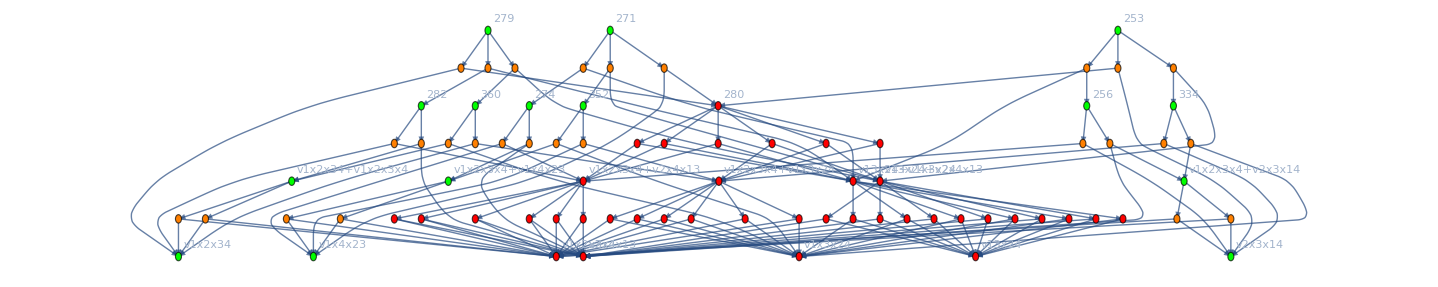

```mathematica
With[
{edges=MakeDephGraph[stubbornForm4,{279,271,253},10000]},
With[
{nodes=Select[Flatten[Map[{#[[1]],#[[2]]}&,edges]],#<1000&]//DeleteDuplicates,nonNodes=DeleteDuplicates[Select[Flatten[Map[{#[[1]],#[[2]]}&,edges]],#>=1000&]]},
Graph[edges,
VertexLabels->Join[
Table[n->If[Length[stubbornForm4[n,"colofour"]]<3,stubbornForm4[n,"colofour"],n],{n,nodes}],
Table[n->"",{n,nonNodes}]
],
GraphLayout->"LayeredDigraphEmbedding",
DirectedEdges->True,
EdgeShapeFunction->GraphElementData[{"HalfFilledArrow","ArrowSize"->0}],
VertexStyle->Join[
Table[n->If[ToString[stubbornForm4[n,"comp"]]=="GreaterEqual",Red,Green],{n,nodes}],
ComputesColors[stubbornForm4,edges,nonNodes]
]]
]
]
```